# Anharmonic Chains

Reference: H. Spohn, Nonlinear fluctuating hydrodynamics for anharmonic chains. J. Stat. Phys. 154, 1191-1227 (2014)

Shoulder potential

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"anharm_chains_altern_mass.m";
```

## Elastic collision

```mathematica
FullSimplify[Solve[{Subscript[m, 1] Subscript[u, 1]+Subscript[m, 2] Subscript[u, 2]==Subscript[m, 1] Subscript[v, 1]+Subscript[m, 2] Subscript[v, 2],1/2 Subscript[m, 1] Subscript[u, 1]^2+1/2 Subscript[m, 2] Subscript[u, 2]^2==1/2 Subscript[m, 1] Subscript[v, 1]^2+1/2 Subscript[m, 2] Subscript[v, 2]^2},{Subscript[v, 1],Subscript[v, 2]}]]
```

{{v_1→u_1,v_2→u_2},{v_1→((m_1-m_2) u_1+2 m_2 u_2)/(m_1+m_2),v_2→(m_1 (2 u_1-u_2)+m_2 u_2)/(m_1+m_2)}}

```mathematica
Subscript[M, mat]={{(Subscript[m, 1]-Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2]),(2 Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2])},{(2 Subscript[m, 1])/(Subscript[m, 1]+Subscript[m, 2]),-(Subscript[m, 1]-Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2])}};
```

```mathematica
Subscript[M, mat]//MatrixForm
```

((m_1-m_2)/(m_1+m_2) | (2 m_2)/(m_1+m_2)
(2 m_1)/(m_1+m_2) | -(m_1-m_2)/(m_1+m_2))

```mathematica
FullSimplify[Eigenvalues[Subscript[M, mat]]]
```

{-1,1}

```mathematica
FullSimplify[{(Subscript[m, 1] Subscript[u, 1]+Subscript[m, 2] Subscript[u, 2])-(Subscript[m, 1] Subscript[v, 1]+Subscript[m, 2] Subscript[v, 2]),(1/2 Subscript[m, 1] Subscript[u, 1]^2+1/2 Subscript[m, 2] Subscript[u, 2]^2)-(1/2 Subscript[m, 1] Subscript[v, 1]^2+1/2 Subscript[m, 2] Subscript[v, 2]^2)}/.{Subscript[v, 1]->First[Subscript[M, mat].{Subscript[u, 1],Subscript[u, 2]}],Subscript[v, 2]->Last[Subscript[M, mat].{Subscript[u, 1],Subscript[u, 2]}]}]
```

{0,0}

```mathematica
(* change in velocity *)
FullSimplify[Subscript[M, mat].{Subscript[u, 1],Subscript[u, 2]}-{Subscript[u, 1],Subscript[u, 2]}]
```

{(2 m_2 (-u_1+u_2))/(m_1+m_2),(2 m_1 (u_1-u_2))/(m_1+m_2)}

```mathematica
(* change in momentum can be expressed in terms of velocity difference *)
FullSimplify[{Subscript[m, 1],Subscript[m, 2]}(Subscript[M, mat].{Subscript[u, 1],Subscript[u, 2]}-{Subscript[u, 1],Subscript[u, 2]})]
(* check momentum conservation *)
FullSimplify[Total[%]]
```

{(2 m_1 m_2 (-u_1+u_2))/(m_1+m_2),(2 m_1 m_2 (u_1-u_2))/(m_1+m_2)}

0

## Import initial data

```mathematica
(* load position data from disk *)
Subscript[r, data,0]=Import["collision_test_field_r0.dat","Real64"]
Length[%]
```

{0.636866,0.681602,0.56421,1.97051,2.56042,0.636615,2.64292,4.04612,2.69371,1.85295,0.700425,0.783242,1.88944,2.07801,2.61432,0.622772}

16

```mathematica
(* average elongation, should be conserved *)
Mean[Subscript[r, data,0]]
```

1.68588

```mathematica
Subscript[q, data,0]=Most[Accumulate[Prepend[Subscript[r, data,0],0]]]
Length[%]
```

{0,0.636866,1.31847,1.88268,3.85319,6.41361,7.05022,9.69314,13.7393,16.433,18.2859,18.9863,19.7696,21.659,23.737,26.3514}

16

```mathematica
(* load momentum data from disk *)
Subscript[p, data,0]=Import["collision_test_field_p0.dat","Real64"]
```

{0.695259,-1.49671,0.404693,-1.0769,0.668085,-2.80978,0.338052,-0.0189182,-0.300148,2.70245,-1.26843,3.56142,0.406422,1.56139,-1.12714,2.3231}

```mathematica
(* expectation value is zero, but not current actual value *)
Mean[Subscript[p, data,0]]
```

0.285178

```mathematica
(* alternating masses *)
Subscript[m, 0,1,val]={1,3};
```

```mathematica
Subscript[mass, val]=Flatten[ConstantArray[Subscript[m, 0,1,val],Length[Subscript[q, data,0]]/2]]
```

{1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3}

```mathematica
(* hard-core potential width *)
Subscript[c, val]=1/2;
```

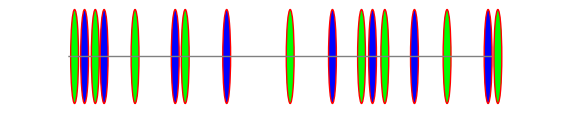

```mathematica
VisualizeField[Accumulate[Prepend[Subscript[r, data,0],0.4]],Append[Subscript[mass, val],First[Subscript[mass, val]]]/Mean[Subscript[m, 0,1,val]],Subscript[c, val],27]
```

```mathematica
(* without taking collisions into account *)
Animate[VisualizeField[Subscript[q, data,0]+0.4+t Subscript[p, data,0]/Subscript[mass, val],Append[Subscript[mass, val],First[Subscript[mass, val]]]/Mean[Subscript[m, 0,1,val]],Subscript[c, val],27],{t,0,10},AnimationRunning->False]
```

## Run simulation

```mathematica
(* example *)
NextCollision[Subscript[r, data,0],Subscript[p, data,0],Subscript[mass, val],Subscript[c, val]]
```

{-1.14549,0.0840812,3}

```mathematica
(* example *)
UpdateField[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[mass, val],Subscript[c, val]];
Differences[First[%]]
```

{0.536459,0.757578,0.5,2.05687,2.4255,0.743789,2.61396,4.02141,2.79468,1.67056,0.906892,0.717598,1.89903,1.93948,2.7742}

```mathematica
Subscript[f, seq]=FieldSequence[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[mass, val],Subscript[c, val],42];
Length[%]
```

43

```mathematica
(* example *)
Subscript[f, seq]⟦{1,2,-1}⟧
```

{{{0,0.636866,1.31847,1.88268,3.85319,6.41361,7.05022,9.69314,13.7393,16.433,18.2859,18.9863,19.7696,21.659,23.737,26.3514},{0.695259,-1.49671,0.404693,-1.0769,0.668085,-2.80978,0.338052,-0.0189182,-0.300148,2.70245,-1.26843,3.56142,0.406422,1.56139,-1.12714,2.3231},0},{{0.0584583,0.594918,1.3525,1.8525,3.90936,6.33486,7.07865,9.69261,13.714,16.5087,18.1793,19.0862,19.8038,21.7028,23.6423,26.4165},{0.695259,-1.49671,-0.740798,0.0685883,0.668085,-2.80978,0.338052,-0.0189182,-0.300148,2.70245,-1.26843,3.56142,0.406422,1.56139,-1.12714,2.3231},0.0840812},{{0.181248,0.828762,1.32876,2.46999,4.6177,7.85091,8.75217,9.66139,12.2281,15.7642,17.1039,22.1484,22.8084,23.5913,24.8994,26.0097},{1.11243,-1.48235,-0.0282638,3.63235,0.724374,3.0705,0.338052,-0.0189182,-0.300148,-2.26763,0.388267,-1.82629,0.351617,1.02434,-1.70125,1.54578},5.03457}}

```mathematica
Interpolation[{Last[#],First[#]}&/@Subscript[f, seq],InterpolationOrder->1]
Animate[VisualizeField[%[t],Subscript[mass, val]/Mean[Subscript[m, 0,1,val]],Subscript[c, val],27],{t,0,3.5},AnimationRunning->False]
```

InterpolatingFunction[{{0., 5.03457}}, <>]

## Compare with C implementation

```mathematica
CollisionInfo[{q_List,p_List,t_},L_,mass_,VdCore_]:=Module[{r=FieldDifferences[q,L],Δt,i},
	{Δt,i}=Rest[NextCollision[r,p,mass,VdCore]];{t+Δt,i}]
```

```mathematica
(* reference *)
Subscript[coll, ref]=CollisionInfo[AdvanceField[#,Subscript[mass, val],0.0001],Total[Subscript[r, data,0]],Subscript[mass, val],Subscript[c, val]]&/@Subscript[f, seq]
Length[%]
```

{{0.0840812,3},{0.114613,1},{0.175406,16},{0.22046,1},{0.318589,2},{0.362796,12},{0.374597,16},{0.423727,3},{0.613676,2},{0.623697,10},{0.957764,14},{1.01456,1},{1.28401,5},{1.38412,13},{1.77489,12},{1.89338,11},{1.89562,4},{2.31947,5},{2.39775,13},{2.66966,15},{2.67652,3},{2.71417,16},{3.23864,14},{3.2539,12},{3.27219,4},{3.45096,1},{3.52157,15},{3.91408,16},{3.98994,13},{4.04069,14},{4.09326,2},{4.18022,1},{4.30064,10},{4.47704,16},{4.5078,12},{4.56951,3},{4.64052,2},{4.66901,13},{4.70367,3},{4.75921,15},{4.86796,12},{5.03457,2},{5.12639,1}}

43

```mathematica
(* load C implementation results from disk *)
"collision_test_event_";
Subscript[coll, test]=Transpose[{(* event times *)Import[%<>"time.dat","Real64"],(* particle indices *)Import[%<>"iprt.dat","Integer32"]+1}];
Length[%]
```

43

```mathematica
(* example *)
Subscript[coll, test]⟦{1,2,-1}⟧
```

{{0.0840812,3},{0.114613,1},{5.12639,1}}

```mathematica
(* compare *)
Norm[Subscript[coll, ref]-Subscript[coll, test]]
```

8.11386×10^-14

```mathematica
(* save reference to disk for comparison *)
"collision_test_ref_event_";
{(* event times *)Export[%<>"time.dat",Subscript[coll, ref]⟦;;,1⟧,"Real64"],(* particle indices *)Export[%<>"iprt.dat",Subscript[coll, ref]⟦;;,2⟧-1,"Integer32"]};
```